# Dünne Linsen

## Laplace

### Berechnung

```mathematica
b = {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}};
g = {{8, 7, 6, 5, 4, 3, 3, 2, 2, 1}};
f = 1/(1/b+1/g)//N;
Grid[{b[[1]],g[[1]],f[[1]]},Frame->All]
```

```mathematica
{{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {8, 5, 6, 5, 4, 3, 3, 2, 2, 1}, {0.8888888888888888, 1.5555555555555556, 2., 2.2222222222222223, 2.2222222222222223, 2., 2.1, 1.6, 1.6363636363636365, 0.9090909090909091}}
```

### Graph

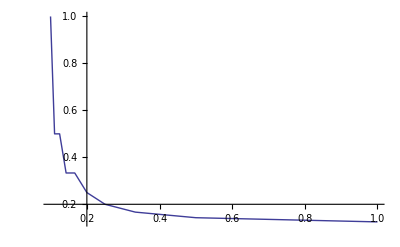

```mathematica
ListLinePlot[Table[{1/b[[1,x]],1/g[[1,x]]},{x,1,Length[b[[1]]]}]]
```